# UCSB Math 3 Series (from Fall 1988)

## Chapter 1

Calculus with Analytical Geometry, 3rd. Edition, Robert Ellis & Denny Gulick

## 1.3 Functions

Definition 1.4: A function consists of a domain and a rule. The domain is a set of real numbers, ℝ. The rule assigns to each number in the domain one and only one number.

#### #11

```mathematica
f[x_]:=x^3-4x+1
```

Find the domain of f.

The domain is all real numbers ℝ or (-∞,∞):

```mathematica
pseudoInfinity =10^10;
interval=Interval[{-pseudoInfinity,pseudoInfinity}];
Plot[f[x],{x,Min[interval],Max[interval]}]
```

-Graphics-

```mathematica
Clear[f,pseudoInfinity,interval]
```

### #13

```mathematica
k[x_]:=1+x^3
```

Find the domain of k for -2 ⩽ x ⩽8.
The domain is [-2,-8]:

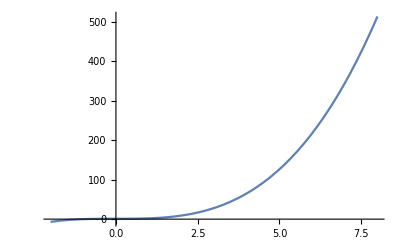

```mathematica
interval=Interval[{-2,8}];
Plot[k[x],{x,Min[interval],Max[interval]}]
```

```mathematica
Clear[k,interval]
```

### #15

```mathematica
f[x_]:=√(x+2)
```

Find the domain of f.

We see that x < -2 is not among ℝ:

```mathematica
test1 = Element[f[-2.1],Reals];
VerificationTest[test1==False]
```

TestResultObject[…]

Alternatively and precisely, we can solve this inequality:

```mathematica
x+2≥0;x+2-2≥0-2
```

x≥-2

The domain is [-2,∞):

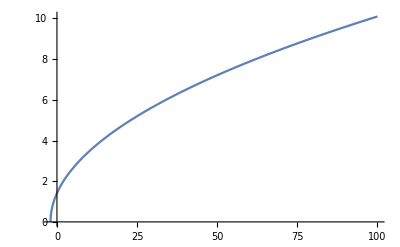

```mathematica
pseudoInfinity =10^2;
interval=Interval[{-2,pseudoInfinity}];
Plot[f[x],{x,Min[interval],Max[interval]}]
```

```mathematica
Clear[f,pseudoInfinity,interval, test1]
```

### #17

```mathematica
f[x_]:=√(x^2+4)
```

Find the domain of f.

```mathematica
x^2+4≥0;x^2+4-4≥0-4; x^2≥-4
```

x^2≥-4

There are no real numbers for the solution to the inequality x^2≥ -4. Without the benefit of complex (or imaginary) numbers, we can say that there are no real numbers bounding x. Alternatively, because x^2 ⩾ 0 for all real numbers ℝ or (-∞,∞), the domain of f is the same:

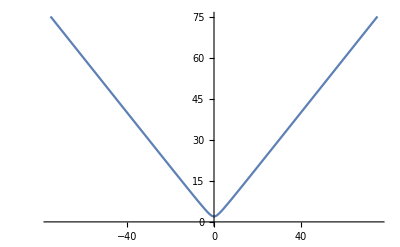

```mathematica
pseudoInfinity =75;
interval=Interval[{-pseudoInfinity,pseudoInfinity}];
Plot[f[x],{x,Min[interval],Max[interval]}]
```

```mathematica
Clear[f,pseudoInfinity,interval]
```

### #19

```mathematica
f[t_]:=√(3-1/t^2)
```

Find the domain of f.

```mathematica
3-1/t^2≥ 0;-1/t^2≥-3;1/t^2≤3;t^2≤1/3;√(t^2)≤ √(1/3);Reduce[√(t^2)≤ √(1/3)]
```

-1/(√3)≤t≤1/(√3)

```mathematica
N[1/(√3)]
```

0.57735

```mathematica
test1 = Element[f[0.4],Reals];
VerificationTest[test1==False]
```

TestResultObject[…]

∴ the domain is (-∞,-√(1/3)] ∪ [√(1/3),∞).

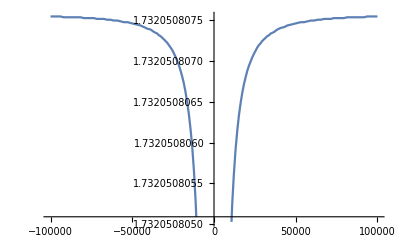

```mathematica
interval1=Interval[{-10^5,-√(1/3)}];
interval2=Interval[{√(1/3),10^5}];
Show[
Plot[f[t],{t,Min[interval1],Max[interval1]}],
Plot[f[t],{t,Min[interval2],Max[interval2]}],
PlotRange->All
]
```

```mathematica
Clear[f,test1,interval1, interval2]
```

### #21

```mathematica
f[t_]:=(1-t^2)^(1/3)
```

Find the domain of f.

```mathematica
1-t^2≥0; -t^2≥-1;t^2≤1;√(t^2)≤ √1
```

√(t^2)≤1

```mathematica
Reduce[√(t^2)≤1]
```

-1≤t≤1

```mathematica
test1 = Element[f[2],Reals];
VerificationTest[test1==False]
```

TestResultObject[…]

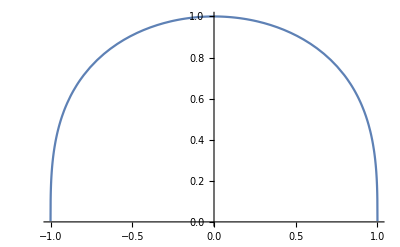

```mathematica
interval=Interval[{-1,1}];
Plot[f[x],{x,Min[interval],Max[interval]}]
```

∴ the domain is [-1,1].

```mathematica
Clear[f,interval, test1]
```

### #23

Find the domain of g.

Find the infinity values excluded from the domain:

```mathematica
Solve[x-1==0,x]
```

{{x→1}}

∴ the domain is (-∞,1) ∪ (1,∞).

```mathematica
VerificationTest[Limit[g[x],Rule[x,1]],∞]
```

TestResultObject[…]

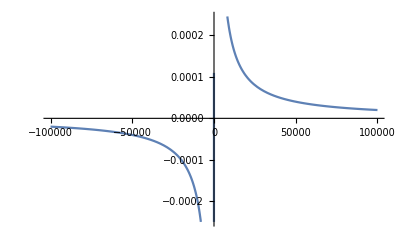

```mathematica
pseudoInfinity =10^5;
interval1=Interval[{-pseudoInfinity,1}];
interval2=Interval[{1,pseudoInfinity}];
Show[
Plot[g[x],{x,Min[interval1],Max[interval1]}],
Plot[g[x],{x,Min[interval2],Max[interval2]}],
PlotRange->All
]
```

```mathematica
Clear[g,pseudoInfinity,interval1, interval2]
```

### #25

```mathematica
g[w_]:=(2w-8)/(w^2-16)
```

Find the domain of g.

```mathematica
(2w-8)/(w^2-16)⇒(2(w-4))/((w+4)(w-4))==2/(4+w);
```

```mathematica
g[w_]:=2/(4+w)
```

Find the infinity values excluded from the domain:

```mathematica
Solve[4+w==0,w]
```

{{w→-4}}

∴ the domain is (-∞,-4) ∪ (-4,∞).

```mathematica
VerificationTest[Limit[g[w],Rule[w,-4]],∞]
```

TestResultObject[…]

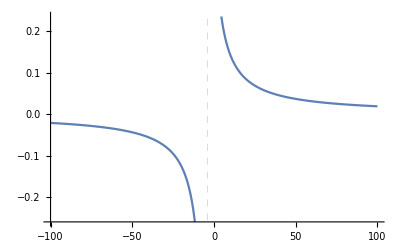

```mathematica
pseudoInfinity =10^2;
interval1=Interval[{-pseudoInfinity,-4}];
interval2=Interval[{-4,pseudoInfinity}];
Show[
Plot[g[w],{w,Min[interval1],Max[interval1]}],
Plot[g[w],{w,Min[interval2],Max[interval2]}],
GridLines->{{{-4,Dashed}},None },
PlotRange->All
]
```

```mathematica
Clear[g,pseudoInfinity,interval1, interval2]
```

### #27

```mathematica
k[x_]:=(2x-3)/(x^2+4)
```

Find the domain of k.

The domain is all real numbers ℝ or (-∞,∞):

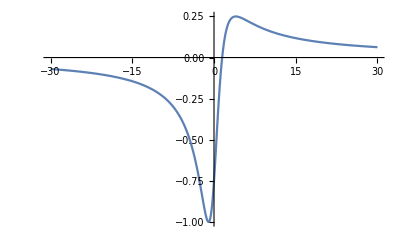

```mathematica
pseudoInfinity =30;
interval=Interval[{-pseudoInfinity,pseudoInfinity}];
Plot[k[x],{x,Min[interval],Max[interval]}]
```

```mathematica
Clear[k,pseudoInfinity,interval]
```

### #29

The function f is

```mathematica
f1[x_]:=2x
```

for -4 ⩽ x ⩽ -1 and

```mathematica
f2[x_]:=3
```

for 0 < x < 6.

Find the domain of f.

The domain is [-4,-1] ∪ (0,6):

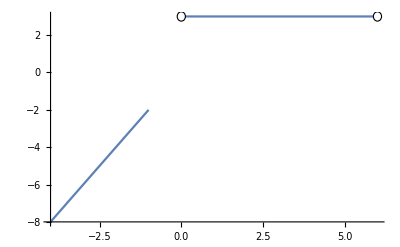

```mathematica
interval1=Interval[{-4,-1}];
interval2=Interval[{0,6}];
Show[
Plot[f1[x],{x,Min[interval1],Max[interval1]}],
Plot[f2[x],{x,Min[interval2],Max[interval2]}],
PlotRange->All,
Epilog->{EdgeForm[Thin],White,Disk[{0,3},{.125,.25}],Disk[{6,3},{.125,.25}]}
]
```

```mathematica
Clear[f1,f2,interval1, interval2]
```

### #31

```mathematica
f[x_]:=√(1-√(9-x^2))
```

Find the domain of f.

```mathematica
9-x^2≤0;9-x^2-9≤0-9;-x^2≤-9;√(x^2)≥ √9
```

√(x^2)≥3

We see that x ⩽ 3 and x ⩾ -3.

```mathematica
VerificationTest[Element[f[3.1],Reals]==False]
```

TestResultObject[…]

```mathematica
√(9-x^2)≤1;(√(9-x^2))^2≤1^2;9-x^2≤1;9-x^2-9≤1-9;-x^2≤-8;√(x^2)≥ √8
```

√(x^2)≥2 √2

```mathematica
N[2 √2]
```

2.82843

We see that 2 √2 ⩽ x ⩽ 3 and -2 √2 ⩾ x ⩾ -3.

```mathematica
VerificationTest[Element[f[2.7],Reals]==False]
```

TestResultObject[…]

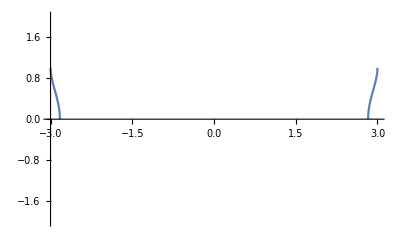

```mathematica
interval1=Interval[{-2 √2,-3}];
interval2=Interval[{2 √2,3}];
Show[
Plot[f[x],{x,Min[interval1],Max[interval1]}],
Plot[f[x],{x,Min[interval2],Max[interval2]}],
PlotRange->{-2,2}
]
```

∴ the domain is [-2 √2,-3] ∪ [2 √2,3]

```mathematica
Clear[f,pseudoInfinity,interval1,interval2]
```